## MaTeX

```mathematica
Needs["MaTeX`"]
```

## Model

### Variables

```mathematica
(*B0 to be determined with regression.*)
R =  0.02; (*Tube radius (m).*)
z1 = 0.0402; (*Distance from first wire loop (m).*)
l = 0.0543; (*Length of solenoid (m).*)
g = 9.8; (*Gravitational acceleration (m/s^2)*)
NT = 397;(*Number of wire turns.*)
```

### Old model

```mathematica
(*We'll remove the constant we are looking to fit (B0) from the field.*)

NormalizedField[z_] := R^3/(R^2+z^2)^(3/2);

(*AccelMotion[t_] := z1 - g t^2/2;
AccelField[t_] := Composition[NormalizedField, AccelMotion][t]
AccelVoltage[t_] := -Pi R^2 AccelField'[t]

minimumTime = t/.FindMinimum[AccelVoltage[t], {t, 0.05}][[-1]]; (*Time of second minimum.*)

(*Shifting voltage so as to have minimumTime = 0*)
AccelVoltage[t_] = AccelVoltage[t+minimumTime];*)
```

### New Model

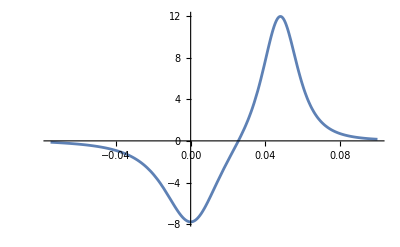

```mathematica
n = 100; (*Number of divisions.*)
z[k_] := z1 + (k-1)l/(n-1) (*Fall distance for each loop.*)
h[t_, k_] := z[k] - g t^2/2  (*Height with respect to z[k] at a given time.*)
AccelField[t_, k_] := Composition[NormalizedField, h][t, k]
AccelVoltage[t_] = -NT Pi R^2 Sum[D[AccelField[t, k]/n, t], {k, 1, n}];

minimumTime = t/.FindMinimum[AccelVoltage[t], {t, 0.05}][[-1]]; (*Time of second minimum.*)

(*Shifting voltage so as to have minimumTime = 0*)
AccelVoltage[t_] = AccelVoltage[t+minimumTime];

Plot[AccelField[t+minimumTime, 20]/n, {t, -1, 1}, PlotRange->All];
Plot[AccelVoltage[t], {t, -0.075, 0.1}, PlotRange->All]
```

## Data

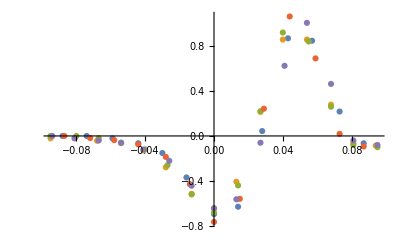

```mathematica
notePath = NotebookDirectory[];
filePath = "\\inputData\\cleaned_small_magnet\\";


fileName = "Cleaned_397_NO_REKT_1.txt";
fullName = StringJoin[{notePath, filePath, fileName}];
data1 = Import[fullName, "Data"];

fileName = "Cleaned_397_NO_REKT_2.txt";
fullName = StringJoin[{notePath, filePath, fileName}];
data2 = Import[fullName, "Data"];

fileName = "Cleaned_397_NO_REKT_3.txt";
fullName = StringJoin[{notePath, filePath, fileName}];
data3 = Import[fullName, "Data"];

fileName = "Cleaned_397_NO_REKT_4.txt";
fullName = StringJoin[{notePath, filePath, fileName}];
data4 = Import[fullName, "Data"];

fileName = "Cleaned_397_NO_REKT_5.txt";
fullName = StringJoin[{notePath, filePath, fileName}];
data5 = Import[fullName, "Data"];

data = Join[data1, data2, data3, data4, data5];
dataPlot = ListPlot[{data1, data2, data3, data4, data5}, PlotRange->All]
```

## Fitting

| Estimate | Standard Error | t-Statistic | P-Value
B0 | 0.0990811 | 0.00256348 | 38.651 | 5.86935×10^-49

-Graphics-

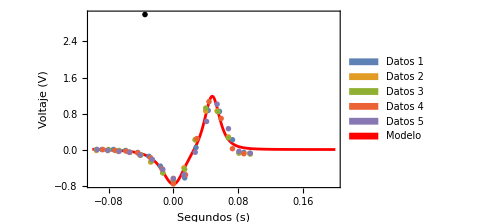

```mathematica
(*We bring back the constant B0. So AccelVoltage is no longer "normalized"*)
AbnormalAccelVoltage[t_] = B0 AccelVoltage[t];

fitModel = NonlinearModelFit[data, AbnormalAccelVoltage[t], B0, t];fitPlot = Plot[fitModel[t], {t, -0.1, 0.2}, PlotStyle->Red, PlotRange->All];

(*Parameters converted from tesla to gauss*)
B0Fitted = 10000 B0/.fitModel["BestFitParameters"];
standardError = 10000 fitModel["ParameterErrors"][[1]];
fitModel["ParameterTable"]

B0FittedFormat = MaTeX[StringJoin[{ToString[B0Fitted],"\\pm",ToString[standardError]}]]
B0Display = MaTeX["B_0 = (1200\\pm200)\\,\mathrm{G}", Magnification->1.2];
B0Graphic = Graphics[Text[B0Display, {-0.035, 3}]];

fullPlot = Show[fitPlot, dataPlot, B0Graphic, Frame->True, FrameLabel->{"Segundos (s)", "Voltaje (V)"}, LabelStyle->Directive[FontFamily->"Times New Roman", FontColor->Black, FontSize->14]];

fullPlot = Legended[fullPlot, Placed[SwatchLegend[{RGBColor["#5e81b5"], RGBColor["#e19c24"], RGBColor["#8fb032"], RGBColor["#eb6235"], RGBColor["#8778b3"], Red}, {"Datos 1", "Datos 2", "Datos 3", "Datos 4", "Datos 5", "Modelo"}, LegendLayout->{"Column",2}, LabelStyle->{FontFamily->"Times New Roman", FontSize->11}, LegendFunction->Panel], {0.77, 0.8}]];

Show[fullPlot, ImageSize->Medium]

(*Export plot.*)
graphicsPath = StringJoin[{notePath,"graphics\\old_model_big_magnet_full.jpg"}];
Export[graphicsPath, fullPlot, ImageResolution->300];
```

### Residuals

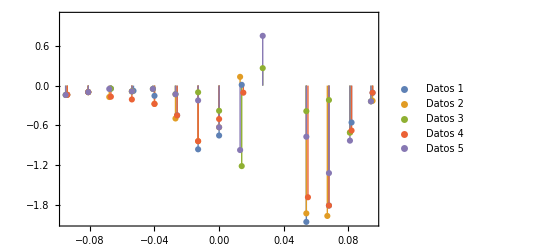

```mathematica
Residuals = fitModel["StandardizedResiduals"];

Residuals1 = Transpose[{data1[[All, 1]], Residuals[[1;;Length[data1]]]}];
Residuals2 = Transpose[{data2[[All, 1]], Residuals[[Length[data1]+1;;Length[data1]+Length[data2]]]}];
Residuals3 = Transpose[{data3[[All, 1]], Residuals[[Length[data1]+Length[data2]+1;;Length[data1]+Length[data2]+Length[data3]]]}];
Residuals4 = Transpose[{data4[[All, 1]], Residuals[[Length[data1]+Length[data2]+Length[data3]+1;;Length[data1]+Length[data2]+Length[data3]+Length[data4]]]}];
Residuals5 = Transpose[{data5[[All, 1]], Residuals[[Length[data1]+Length[data2]+Length[data3]+Length[data4]+1;;-1]]}];

ListPlot[{Residuals1, Residuals2, Residuals3, Residuals4, Residuals5}, Filling->Axis, FillingStyle->Thick, PlotLegends->{"Datos 1", "Datos 2", "Datos 3", "Datos 4", "Datos 5"}, Frame->True]
```